```mathematica
Clear["Global`*"];
Off[General::spell];
Off[General::spell1];
```

```mathematica
m=3;
d=5;
```

```mathematica
sol=ParametricNDSolve[{x'[t]==y[t],y'[t]==m*(1-x[t]^2)*y[t]-x[t]+d*Cos[w*t]},{x,y},{t,300,400},{w},Method->{"IndexReduction"->Automatic}]
```

{x→ParametricFunction[<>],y→ParametricFunction[<>]}

ParametricNDSolve::ndcf: Repeated convergence test failure at t$782294 == 0.0812363; unable to continue.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t$782294 == 300. and t$782294 == 400..

ParametricNDSolve::ndsz: At t$782294 == 0.323266, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t$782294 == 300. and t$782294 == 400..

ParametricNDSolve::ndsz: At t$782294 == 1.00042, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of ParametricNDSolve :: ndsz will be suppressed during this calculation.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t$782294 == 300. and t$782294 == 400..

General::stop: Further output of NDSolve`ProcessSolutions :: nodata will be suppressed during this calculation.

ParametricNDSolve::ndcf: Repeated convergence test failure at t$782294 == 0.0812363; unable to continue.

General::stop: Further output of ParametricNDSolve :: ndcf will be suppressed during this calculation.

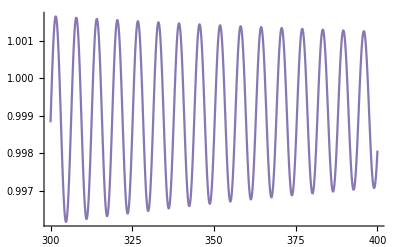

```mathematica
Plot[Evaluate[Table[x[w][t]/.sol,{w,{20,5,2,1.788,1}}]],{t,300,400},PlotRange->All]
```

Only ω=1 has solutions in that region out of the given values for ω.

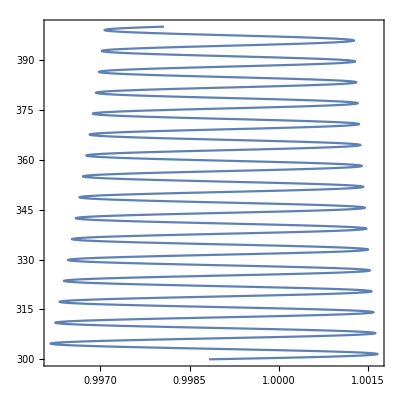

```mathematica
Show[ParametricPlot[{x[1][t]/.sol,y[1][t]/.sol},{t,300,400}],
Frame -> True, 
AspectRatio -> 1]
```